```mathematica
Clear["Global`*"];
```

```mathematica
QQ=10^-9;(*C*)
ϵ0=8.85×10^-12;(*F/m*)
```

```mathematica
Geometry={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};
HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry,MaxCellMeasure->0.05]],Labeled[0,"Index"]]
NEl=MeshCellCount[%,1]
```

-Graphics-

102

```mathematica
GreenF[x_,x0_]:=-N[1/(2 π) Log[Norm[x-x0]]];
DGreenF[x_,x0_]:=-N[1/(2 π Norm[x-x0])];
```

```mathematica
BElts=MeshPrimitives[bMesh,1];
Knots=RegionCentroid/@MeshPrimitives[bMesh,1];
TriangleInd=Select[Range[NEl],6≥ Knots[[#,1]]≥ 2 && -1.5≤ Knots[[#,2]]≤1 &];
RectangleInd=Select[Range[NEl],Knots[[#,1]]≥ 0.9 && 1.5≤ Knots[[#,2]]≤4.5 &];
DiskInd= Select[Range[NEl],Knots[[#,1]]≤1 && Knots[[#,2]]≤1 &];
```

```mathematica
BElts=Join[BElts[[RectangleInd]],BElts[[TriangleInd]],BElts[[DiskInd]]];
Knots=RegionCentroid/@BElts;
Measure=RegionMeasure/@BElts;
Segment=ParallelTable[BElts[[i,1,2]]-BElts[[i,1,1]],{i,1,NEl}];
TriangleInd=Select[Range[NEl],6≥ Knots[[#,1]]≥ 2 && -1.5≤ Knots[[#,2]]≤1 &];
RectangleInd=Select[Range[NEl],Knots[[#,1]]≥ 0.9 && 1.5≤ Knots[[#,2]]≤4.5 &];
DiskInd= Select[Range[NEl],Knots[[#,1]]≤1 && Knots[[#,2]]≤1 &];
```

```mathematica
G=ParallelTable[If[i!=j,NIntegrate[GreenF[Knots[[i]],BElts[[j,1,1]]+t Segment[[j]]],{t,0,1}],0],{i,1,NEl},{j,1,NEl}];
G=Transpose[Measure×Transpose[G]]+DiagonalMatrix[Table[#/π(1-Log[#])&[Measure[[i]]/2] ,{i,1,NEl}]];
G=Chop[G];
```

```mathematica
Off[NIntegrate::izero];
H=Transpose[
Measure×
Transpose[ParallelTable[If[i!=j,NIntegrate[({-#[[2]],#[[1]]}/Measure[[j]]&[Segment[[j]]]).(#/Norm[#]&[BElts[[j,1,1]]+t Segment[[j]]-Knots[[i]]])DGreenF[Knots[[i]],BElts[[j,1,1]]+t Segment[[j]]],{t,0,1}],0],{i,1,NEl},{j,1,NEl}]]];
H=H+1/2 IdentityMatrix[NEl];
H=Chop[H];
```

```mathematica
Subscript[G, RR]=G[[RectangleInd,RectangleInd]];
Subscript[G, RT]=G[[RectangleInd,TriangleInd]];
Subscript[G, RD]=G[[RectangleInd,DiskInd]];
Subscript[G, TR]=G[[TriangleInd,RectangleInd]];
Subscript[G, TT]=G[[TriangleInd,TriangleInd]];
Subscript[G, TD]=G[[TriangleInd,DiskInd]];
Subscript[G, DR]=G[[DiskInd,RectangleInd]];
Subscript[G, DT]=G[[DiskInd,TriangleInd]];
Subscript[G, DD]=G[[DiskInd,DiskInd]];
```

```mathematica
Subscript[H, RR]=H[[RectangleInd,RectangleInd]];
Subscript[H, RT]=H[[RectangleInd,TriangleInd]];
Subscript[H, RD]=H[[RectangleInd,DiskInd]];
Subscript[H, TR]=H[[TriangleInd,RectangleInd]];
Subscript[H, TT]=H[[TriangleInd,TriangleInd]];
Subscript[H, TD]=H[[TriangleInd,DiskInd]];
Subscript[H, DR]=H[[DiskInd,RectangleInd]];
Subscript[H, DT]=H[[DiskInd,TriangleInd]];
Subscript[H, DD]=H[[DiskInd,DiskInd]];
```

```mathematica
(*G==Join[Join[Subscript[G, RR],Subscript[G, RT],Subscript[G, RD],2],Join[Subscript[G, TR],Subscript[G, TT],Subscript[G, TD],2],
Join[Subscript[G, DR],Subscript[G, DT],Subscript[G, DD],2]];*)
```

```mathematica
qRv=ParallelTable[Subscript[qR, i],{i,1,Length[RectangleInd]}];
qTv=ParallelTable[Subscript[qT, i],{i,1,Length[TriangleInd]}];
qDv=ParallelTable[2,{i,1,Length[DiskInd]}];
```

```mathematica
uRv=ParallelTable[1,{i,1,Length[RectangleInd]}];
uTv=ParallelTable[Subscript[uT, i],{i,1,Length[TriangleInd]}];
uDv=ParallelTable[Subscript[uD, i],{i,1,Length[DiskInd]}];
```

```mathematica
A=ParallelTable[
If[i==j,1,If[i==j-1,-1,0]]
,{i,1,Length[TriangleInd]-1},
{j,1,Length[TriangleInd]}];
```

```mathematica
B=ParallelTable[Cross[
Append[({-#[[2]],#[[1]]}/Measure[[i]]&[Segment[[i]]]),0],
Append[Segment[[i]],0]
][[3]],{i,TriangleInd},{j,1,1}];
```

```mathematica
LeftMatrix=Join[
Join[Subscript[G, RR],Subscript[G, RT],-Subscript[H, RD],-Subscript[H, RT],2],
Join[Subscript[G, TR],Subscript[G, TT],-Subscript[H, TD],-Subscript[H, TT],2],
Join[Subscript[G, DR],Subscript[G, DT],-Subscript[H, DD],-Subscript[H, DT],2],
Join[Table[0,{i,1,1},{j,1,Length[RectangleInd]}],Transpose[B],Table[0,{i,1,1},{j,1,Length[DiskInd]+Length[TriangleInd]}],2],
Join[Table[0,{i,1,Length[TriangleInd]-1},{j,1,NEl}],A,2]
];
```

```mathematica
RightMatrix=Join[
Join[Subscript[H, RR],-Subscript[G, RD],2],
Join[Subscript[H, TR],-Subscript[G, TD],2],
Join[Subscript[H, DR],-Subscript[G, DD],2],
Table[0,{i,1,Length[LeftMatrix]-NEl},{j,1,Length[RectangleInd]+Length[DiskInd]}]
];
```

```mathematica
Charge=Join[
Table[0,{i,1,NEl}],
{-QQ/ϵ0},
Table[0,{i,1,Length[TriangleInd]-1}]
];
```

```mathematica
s=LinearSolve[LeftMatrix,RightMatrix.Join[uRv,qDv]+Charge];
```

```mathematica
qRv=s[[1;;Length[RectangleInd]]];
qTv=s[[1+Length[RectangleInd];;Length[TriangleInd]+Length[RectangleInd]]];
uDv=s[[1+Length[TriangleInd]+Length[RectangleInd];;Length[DiskInd]+Length[TriangleInd]+Length[RectangleInd]]];
uTv=s[[1+Length[DiskInd]+Length[TriangleInd]+Length[RectangleInd];;Length[TriangleInd]+Length[DiskInd]+Length[TriangleInd]+Length[RectangleInd]]];
```

```mathematica
u=Join[uRv,uTv,uDv];
q=Join[qRv,qTv,qDv];
```

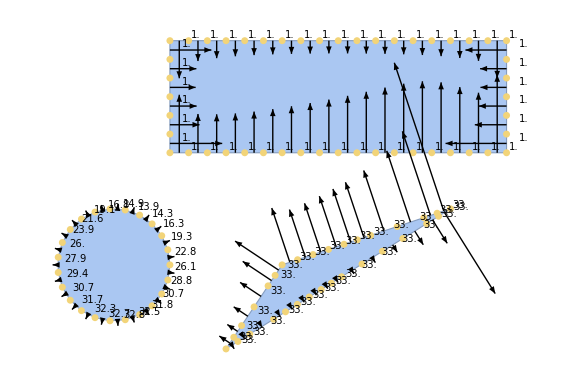

```mathematica
Show[
HighlightMesh[bMesh,0,ImageSize->Large],
Graphics[{
Arrowheads[.02],
ParallelTable[
Arrow[{
Knots[[i]],
Knots[[i]]-0.05×q[[i]]{-#[[2]],#[[1]]}/Norm[#]&[Segment[[i]]]
}],
{i,1,NEl}]}
],
Graphics[ParallelTable[Text[Style[Round[u[[i]],0.1],Black,10],Knots[[i]]+{0.3,0.1}],{i,1,NEl}]]]
```